In this notebook we check the Ising solution on 1D.

```mathematica
energies3 = Table[{g,J}={1,j};
z = PauliMatrix[3];
x=PauliMatrix[1];
id = IdentityMatrix[2];
h = -(g)*(KroneckerProduct[KroneckerProduct[z, id], id] + KroneckerProduct[KroneckerProduct[id, id], z]+ KroneckerProduct[ KroneckerProduct[id, z], id] )+ -(J)*(KroneckerProduct[KroneckerProduct[x, x], id] + KroneckerProduct[KroneckerProduct[id, x], x]+ KroneckerProduct[ KroneckerProduct[x, id], x]);
k = h//Eigenvalues;
{j,k[[1]]}
,{j,.01,4.1,.4}]
```

{{0.01,-3.00008},{0.41,-3.15138},{0.81,-3.64967},{1.21,-4.44973},{1.61,-5.42574},{2.01,-6.49144},{2.41,-7.60433},{2.81,-8.744},{3.21,-9.90003},{3.61,-11.0667},{4.01,-12.2405}}

```mathematica
energies3
```

{{0.01,-3.00008},{0.41,-3.15138},{0.81,-3.64967},{1.21,-4.44973},{1.61,-5.42574},{2.01,-6.49144},{2.41,-7.60433},{2.81,-8.744},{3.21,-9.90003},{3.61,-11.0667},{4.01,-12.2405}}

Now the analytic solution some L

```mathematica
Divisible[8,2]
```

True

```mathematica
L=3;
Kp1 = Table[
2*n*Pi/L,{n,1,(L-1)/2}];
Kp0 =Union[ Table[(((2*n)-1)*Pi)/L,{n,1,(L-1)/2}],Table[(((2*n)-1)*Pi)/L,{n,-(L-1)/2,0}]];
totalK={};
Do[j=Kp1[[k]];
If[j==0 || j==Pi||j==-Pi,None,AppendTo[totalK,j]],{k,1,Length[Kp1]}];
totalK;
e[k_,J_,h_]:=-2*J*Sqrt[(Cos[k]-h/J)^2+(Sin[k])^2];
eg[J_,h_]:=(
gg=-2*J;
Do[it=totalK[[r]];
If[0<it<Pi,gg=gg+e[it,J,h]],{r,1,Length[totalK]}];gg);
enAn=Table[{j,eg[j,1]},{j,.01,4.1,.4}];
enAn
```

{{0.01,-2.03007},{0.41,-3.33245},{0.81,-4.76076},{1.21,-6.25359},{1.61,-7.78162},{2.01,-9.3304},{2.41,-10.8923},{2.81,-12.4628},{3.21,-14.0395},{3.61,-15.6205},{4.01,-17.2048}}

```mathematica
totalK
```

{(2 π)/3}

```mathematica
e[totalK[[1]], 0.01,1]
```

-2.01007

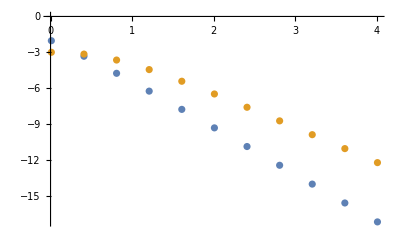

```mathematica
ListPlot[{enAn,energies3}]
```